#### Read Tweets

```mathematica
twitter = Import["/Users/dalila/data/twitter_text_0622_1931pm.xls","XLS"];
```

```mathematica
twitter = twitter[[1]];
```

Dataset dimension

```mathematica
Dimensions[twitter]
```

{12276,4}

```mathematica
twitter[[1;;3]]
```

We decided some of these words either represent places in UK or are the long version of the word UK

```mathematica
countryToChoose = {"kingdom","england","coventry","poole","leicestershire","london","uk"}
```

{kingdom,england,coventry,poole,leicestershire,london,uk}

Make twitter lower case, seperate the headings from the data

```mathematica
twitter = Map[Map[ToLowerCase[#]&,#]&,twitter];
```

```mathematica
twitterHeading = First[twitter];
```

```mathematica
twitterData = Rest[twitter];
```

#### Get only UK tweets, and remove handels and URL links

```mathematica
onlyUK = Select[twitterData,StringContainsQ[#[[2]],{"kingdom","england","coventry","poole","leicestershire","london","uk"}]&];
```

```mathematica
twitterHand = Map[TextCases[#[[1]],"TwitterHandle"]&,onlyUK]
```

```mathematica
twitt= MapThread[StringDelete,{onlyUK[[All,1]],twitterHand} ];
```

```mathematica
twitt = Map[StringDelete[#,TextCases[#,"URL"]]&,twitt]
```

Save tweets after removing the twitter handle and the urls’

```mathematica
Save["brexitTweets",twitt]
```

```mathematica
Export["/Users/dalila/data/clean.xls",twitt]
```

/Users/dalila/data/clean.xls

#### Tokenize tweets, remove stop words, and stem words

```mathematica
cleanData = Map[WordStem[DeleteStopwords[TextWords[#]]]&,twitt];
```

```mathematica
(*Remove Duplicates*)
cleanData=Tally[cleanData][[All,1]]
```

#### Remove non words from the corrupt tweets. Remove underscores, the words rt, amp, and exit

```mathematica
cleanData = Map[StringReplace[#,"_"->""]&,cleanData];
cleanData = Map[StringReplace[#,"-"->""]&,cleanData];
```

```mathematica
cleanData =Map[Select[#,!StringContainsQ[#,RegularExpression["[^a-z0-9\#\'\-]+"]]&]&,cleanData];
```

```mathematica
f[l_] := Select[l,#≠"rt"&];
```

```mathematica
cleanData =Map[f[#]&,cleanData]
```

```mathematica
f[l_] := Select[l,#≠"amp"&];
cleanData =Map[f[#]&,cleanData]
```

```mathematica
Select[cleanData,MemberQ[#,"exit"]&]
```

```mathematica
Length[cleanData]
```

1668

#### Get words in all the tweets, and create a frequency bar chart

One notices that 7 words dominate the tweets chatter

```mathematica
tp = Flatten[cleanData]
```

```mathematica
tallyTweet = Reverse[SortBy[Tally[tp],Last]];
```

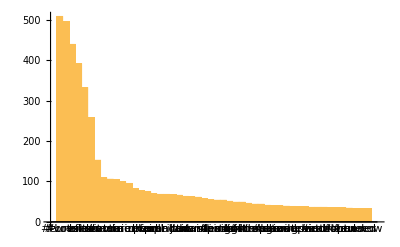

```mathematica
BarChart[Apply[Labeled,Reverse[%414[[1;;50]],2],{1}]]
```

```mathematica
Length[tallyTweet]
```

3466

#### The 50 most common words in the tweet One notices that leave and its derivatives are in higher frequency than remain derivatives

```mathematica
tallyTop50= Reverse[SortBy[tallyTweet,Last]][[1;;50]]
tallyTop50 = SortBy[tallyTop50,Last]
tallyName = tallyTop50[[1;;50,1]];
tallyFreq = tallyTop50[[1;;50,2]];
```

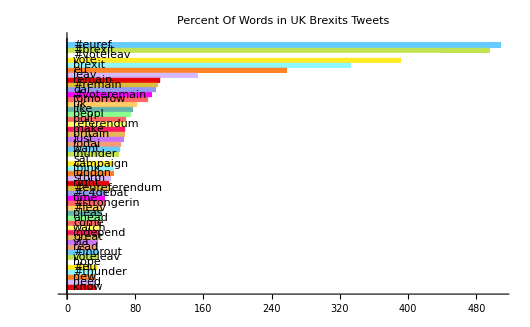

```mathematica
BarChart[tallyFreq,BarOrigin->Left,ChartLabels->{Placed[tallyName,Left]},LabelingFunction->None,PlotLabel->"Percent Of Words in UK Brexits Tweets" ,ChartStyle->60,BarSpacing-> Automatic]
```

Initial WordCloud, before combining synonyms

You will notice that Voteleave dominate voteremaine, or remain.  You also notice that many words represent the same thing (remain, voteremain, #remain, etc.)

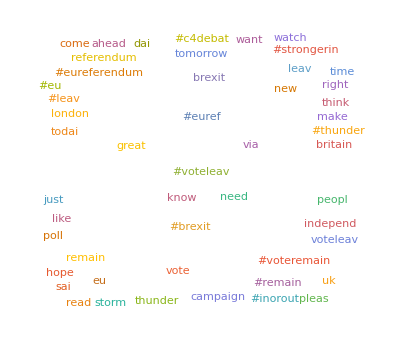

```mathematica
WordCloud[tallyTop50]
```

```mathematica
Grid[%521]
```

#euref | 508
#brexit | 495
#voteleav | 439
vote | 391
brexit | 332
eu | 257
leav | 153
remain | 109
#remain | 106
dai | 104
#voteremain | 99
tomorrow | 95
uk | 82
like | 77
peopl | 74
poll | 69
referendum | 68
make | 68
britain | 67
just | 66
todai | 63
want | 62
thunder | 61
sai | 57
campaign | 55

#### Same words for leave. All these words are related to leave. Removed one word dontleav, which should be with remain

```mathematica
leaveWords =Tally[Select[tp,StringContainsQ[#,___~~"leav"~~___]&]][[All,1]]
```

{#voteleav,voteleav,leav,leavetheeu,leaveeuoffici,#beleav,beleav,#leav,#labourleav,#leaveeu,#voteleavetakebackcontrol,italeav,#loveeuropeleaveeu,#voteleavetakecontrol,leave-eu,#liberalleav,#leaveemtoit,#fishingforleav,#shakeitandleav,#dontleav,leavemedia,ukleaveeu,#votetoleav,#voteleave4uma,#ukleaveeucampaign,labourleav,#leavelillyleav}

```mathematica
leaveWords ={"#voteleav","voteleav","leav","leavetheeu","leaveeuoffici","#beleav","beleav","#leav","#labourleav","#leaveeu","#voteleavetakebackcontrol","italeav","#loveeuropeleaveeu","#voteleavetakecontrol","leave-eu","#liberalleav","#leaveemtoit","#fishingforleav","#shakeitandleav","leavemedia","ukleaveeu","#votetoleav","#voteleave4uma","#ukleaveeucampaign","labourleav","#leavelillyleav","pro-brexit","leaveeu","leavetheu", "leaveofficial"};
```

```mathematica
Save["cleanDataBrexit",cleanData]
```

#### Find synonyms to referendum, remain, and brexit

```mathematica
Tally[Select[tp,StringContainsQ[#,___~~"ref"~~___]&]][[All,1]]
```

```mathematica
referendumWord = {"#euref","referendum","referend---world","#eureferendum","#referendum","indyref","ref","euref","#ukreferendum","eureferendum","referundum"}
```

{#euref,referendum,referend---world,#eureferendum,#referendum,indyref,ref,euref,#ukreferendum,eureferendum,referundum}

```mathematica
remainWords =Tally[Select[tp,StringContainsQ[#,___~~"remain"~~___]&]][[All,1]]
```

```mathematica
{"#voteremain","remain","#remain","#bremain","#remainineu","bremain","#remainathom","#iminsanevoteremain","#remainin","dontleav"}
```

```mathematica
remainWords = Join[remainWords,{"#dontleav"}]
```

```mathematica
Select[twitterData[[All,1]],StringContainsQ[#,__~~"#brexitdeb"~~__]&]
```

```mathematica
Tally[Select[tp,StringContainsQ[#,___~~"brexit"~~___]&]]
```

```mathematica
brexitWords={{"#brexit",495},{"brexit",332},{"brexit-",2},{"#brexitornot",6},{"brexit'",3},{"#brexitdeb",4},{"#brexitfact",1},{"#brexitclub",2}}
```

```mathematica
brexitWords= brexitWords[[All,1]]
```

#### Now, we can draw a WordCloud, but first we need to combine all the words that are the same

```mathematica
tp = StringReplace[tp,{leaveWords  -> "leav",remainWords-> "remain",referendumWord -> "referendum",brexitWords->"#brexit",ukWord-> "uk",euWord->"eu"}]
```

```mathematica
ukWord = {"uk","britain","#uk","british"};
```

```mathematica
euWord = {"#eu","europe","europ"}
```

{#eu,europe,europ}

```mathematica
Tally[Select[tp,StringContainsQ[#,___~~"referend"~~___]&]][[All,1]]
```

Some other words we found that are related to referendum

```mathematica
referWord = {"referendumorm","referendumerendum","referendumus","referendumerundum"}
```

{referendumorm,referendumerendum,referendumus,referendumerundum}

```mathematica
tp = StringReplace[tp,{leaveWords  -> "leav",remainWords-> "remain",referendumWord -> "referendum",brexitWords->"#brexit",ukWord-> "uk",euWord->"eu",referWord->"referendum"}];
```

```mathematica
tp = StringReplace[tp,"leaveeu"-> "leav"]
```

```mathematica
tp = StringReplace[tp,"#london"-> "london"]
```

```mathematica
tp = StringReplace[tp,"#"-> ""]
```

#### Tally the words in all cleaned tweets

```mathematica
tallyTweet = Reverse[SortBy[Tally[tp],Last]]
```

One can see that word leave comes second only brexit and its frequency is more than twice that of remain

```mathematica
tmp = SortBy[tallyTweet[[1;;25]],Last]
```

{{strongerin,45},{c4debat,47},{right,49},{think,54},{campaign,55},{sai,57},{want,62},{todai,63},{storm,64},{just,66},{make,68},{poll,70},{peopl,74},{like,77},{london,78},{thunder,95},{tomorrow,95},{dai,105},{uk,200},{eu,321},{remain,334},{vote,397},{referendum,670},{leav,728},{brexit,827}}

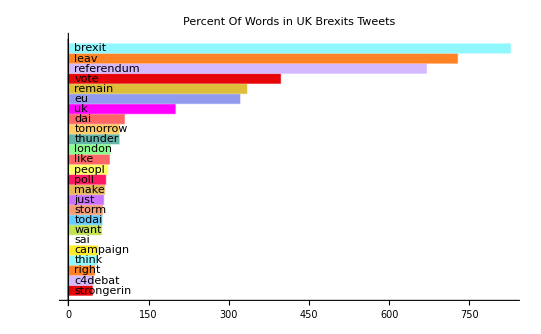

```mathematica
BarChart[tmp[[All,2]],BarOrigin->Left,ChartLabels->{Placed[tmp[[All,1]],Left]},LabelingFunction->(Placed[Panel[tmp[[All,1]],FrameMargins->0],Above]),PlotLabel->"Percent Of Words in UK Brexits Tweets" ,ChartStyle->60,BarSpacing-> Automatic]
```

#### The WordCloud reinforce the predominence of Leave. One can also notice

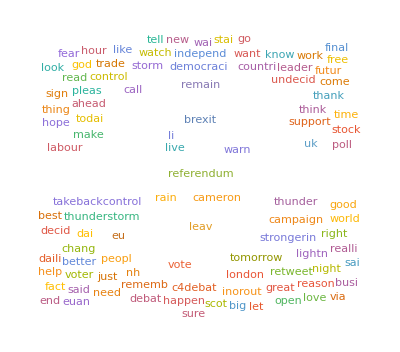

```mathematica
WordCloud[tp]
```

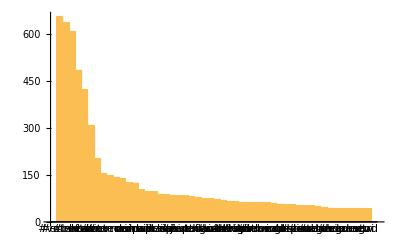

```mathematica
BarChart[Apply[Labeled,Reverse[%376,2],{1}]]
```

```mathematica
uniqueLocations=Select[uniqueLocations,!MemberQ[StringMatchQ[#,WordBoundary~~DigitCharacter.. ~~WordBoundary],True]&]
```

```mathematica
uniqueLocations= DeleteCases[uniqueLocations,{}]
```

```mathematica
countryRule = {"kingdom"-> "uk","england"-> "uk","coventry"-> "uk","poole"-> "uk","leicestershire"->"uk","london"->"uk","leeds"-> "uk","glasgow"->"uk","sheffield"-> "uk","bradford"-> "uk","manchester"->"uk","liverpool"->"uk","edinburgh"-> "uk","bristol"->"uk","scotland"->"uk","wales"->"uk","northern ireland"}
{"19600858","99047821"}
```

{kingdom→uk,england→uk,coventry→uk,poole→uk,leicestershire→uk,london→uk}

{19600858,99047821}

#### Now we Go back to Clean Data and remove unecessary words, and get ready for graph network

```mathematica
word2Remove = {{"87rt",1},{"847",1},{"75",1},{"6k",1},{"60bn",1},{"60",1},{"5h",1},{"5am-7am",1},{"58-42",1},{"5000",1},{"50",1},{"49",1},{"46",1},{"43",1},{"41",1},{"3rd",1},{"3k",1},{"38",1},{"33",1},{"322278",1},{"32",1},{"2mrw",1},{"2moro",1},{"28th",1},{"28",1},{"256",1},{"25",1},{"20yr",1},{"2040",1},{"2020",1},{"2015",1},{"2010-2016",1},{"2008",1},{"1987",1},{"1982",1},{"1951",1},{"17th-22nd",1},{"17",1},{"16",1},{"11pm",1},{"10p",1},{"10a",1},{"1066",1},{"103",1},{"10",1},{"01223",1},{"007",1},{"''",1},
{"'",1},{"-",1}}
```

{{87rt,1},{847,1},{75,1},{6k,1},{60bn,1},{60,1},{5h,1},{5am-7am,1},{58-42,1},{5000,1},{50,1},{49,1},{46,1},{43,1},{41,1},{3rd,1},{3k,1},{38,1},{33,1},{322278,1},{32,1},{2mrw,1},{2moro,1},{28th,1},{28,1},{256,1},{25,1},{20yr,1},{2040,1},{2020,1},{2015,1},{2010-2016,1},{2008,1},{1987,1},{1982,1},{1951,1},{17th-22nd,1},{17,1},{16,1},{11pm,1},{10p,1},{10a,1},{1066,1},{103,1},{10,1},{01223,1},{007,1},{'',1},{',1},{-,1}}

```mathematica
word2Remove = word2Remove[[All,1]]
```

{87rt,847,75,6k,60bn,60,5h,5am-7am,58-42,5000,50,49,46,43,41,3rd,3k,38,33,322278,32,2mrw,2moro,28th,28,256,25,20yr,2040,2020,2015,2010-2016,2008,1987,1982,1951,17th-22nd,17,16,11pm,10p,10a,1066,103,10,01223,007,'',',-}

#### Make sure to have a new version with synonyms taken into account

```mathematica
cleanData = Map[StringReplace[#,word2Remove ->""]&,cleanData]
```

```mathematica
clean2Data = Map[StringReplace[#,{leaveWords  -> "leav",remainWords-> "remain",referendumWord -> "referendum",brexitWords->"#brexit",ukWord-> "uk",euWord->"eu",referWord->"referendum"}]&,cleanData];
clean2Data = Map[StringReplace[#,"leaveeu"-> "leav"]&,clean2Data]
clean2Data= Map[StringReplace[#,"#london"-> "london"]&,clean2Data]
clean2Data = Map[StringReplace[#,"#"-> ""]&,clean2Data]
```

#### Make sure to remove duplicates. Now we are ready for the next analysis

```mathematica
clean2Data = Map[DeleteDuplicates[#]&,clean2Data]
```

```mathematica
Save["FinalCleanBrexit",clean2Data]
```

#### Now, we can start the interesting part: Graph the tweets, and cluster the graph

#### This code is to create undirected graphs from lists

```mathematica
f[re_List] :=Module[{flatTread,i,j},Flatten[Map[(Thread[#->#,#])&,re ]];
flatTread = Table[Thread[re[[i]]->  re[[j]]],{i,Length[re-1]},{j,i+1,Length[re]}];
flatTread = Flatten[flatTread];
UndirectedEdge @@@ flatTread]
```

Sample example

```mathematica
e1 = f[clean2Data[[1]]];
e2 = f[clean2Data[[2]]];
Dimensions[e1];
t = {e1,e2};
r =Flatten[t];
r = DeleteDuplicates[r]
```

{brexit<->episod,brexit<->delai,brexit<->thur,brexit<->share,brexit<->like,brexit<->hell,episod<->delai,episod<->thur,episod<->share,episod<->like,episod<->hell,delai<->thur,delai<->share,delai<->like,delai<->hell,thur<->share,thur<->like,thur<->hell,share<->like,share<->hell,like<->hell}

Create graphs for all tweets

```mathematica
result = Map[f,clean2Data];
result = Flatten[result];
result = DeleteDuplicates[result];
Dimensions[result]
```

{40300}

Draw graph with Spring Embedding (this is similar to clustering in graph space.  You notice the interesting shape of the graph.  We have 7 regions with high density and few words outside the graph network.  We can also see if we can find cliques, or how big is the largest clique

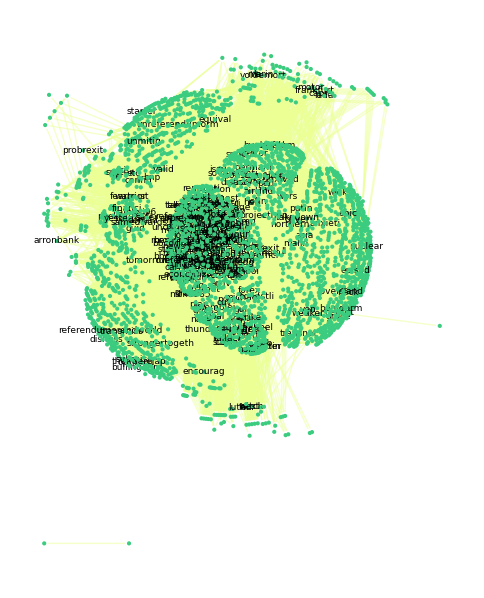

```mathematica
sg = Graph[result,{VertexLabels-> Placed ["Name",Center],EdgeStyle->RGBColor[0.92,1.,0.58],VertexStyle-> RGBColor[0.23,0.8,0.5],VertexLabelStyle->Directive[FontFamily->"Arial",9,Black]},GraphLayout->"SpringEmbedding"]
```

```mathematica
Thread
```

#### Sentiment Analysis and Profanity

clean the tweets text

```mathematica
txtRm =Map[StringDelete[#,{"rt",":","amp"}]&,twitt]
```

#### How many messages had sentiments (903), and how many had profanity(54). Show one remove profanities? Yes

We expected to find more tweets with sentiments, still this number represents more than 50% of all tweets

```mathematica
Length[DeleteCases[Map[TextCases[#,"PositiveSentiment"]&,txtRm],{}]]
```

903

```mathematica
Length[DeleteCases[Map[TextCases[#,"Profanity"]&,txtRm],{}]]
```

54

```mathematica
positiveBrexit =DeleteCases[Map[TextCases[#,"PositiveSentiment"]&,txtRm],{}];
```

```mathematica
txtRm = Map[StringReplace[#,RegularExpression["[e]{2,10}"]-> "e"]&,txtRm];
```

```mathematica
txtRm= Map[StringReplace[#,leaveWords -> "leav"]&,txtRm]
```

```mathematica
txtRm= Map[StringDelete[#,RegularExpression["[^a-z0-9\\s\#\'\-]+"]]&,txtRm]
```

```mathematica
txtRm= Map[StringReplace[#,word2Remove ->""]&,txtRm]
txtRm = Map[StringReplace[#,{leaveWords  -> "leav",remainWords-> "remain",referendumWord -> "referendum",brexitWords->"#brexit",ukWord-> "uk",euWord->"eu",referWord->"referendum"}]&,txtRm];
txtRm = Map[StringReplace[#,"leaveeu"-> "leav"]&,txtRm];
txtRm= Map[StringReplace[#,"#london"-> "london"]&,txtRm];
txtRm= Map[StringReplace[#,"#"-> ""]&,txtRm];
txtRm= Map[StringReplace[#,"byebyeuk"-> "leav"]&,txtRm];
txtRm= Map[StringReplace[#,"leav"-> "leave"]&,txtRm]
```

```mathematica
Select[txtRm,StringContainsQ[#,"remainathom"]&]
```

{in tomorrows referendum make sure you leavemtoit and remainathome}

```mathematica
Save["cleantxtBrexit",txtRm]
```

```mathematica
Length[clean2Data]
```

1668

### Clustering

#### We can either use the Jacquard or Cosine. Still we have to write our own code for both distance measure

Jacquard dissimilarity distance =  n01+n10/(n11+n01+n10) 
(Length[SetA⊂SubB]+Length[SetB⊂SubA])/(Length[SetA⊂SetB]+Length[SetA⊂SetB]+Length[SetA∩SetB]).  In here we modified it to take into consideration the length of the tweets.  If a tweet is a subset to another tweet, than one should expect the distance between it and the longest tweet to be 0.

```mathematica
myDistance [u_,v_] := If[Length[u] == Length [v],(Length[Complement[u,v]]+Length[Complement[v,u]])/(Length[Intersection[u,v]]+Length[Complement[u,v]]+Length[Complement[v,u]]),If[Length[u] < Length[v], Length[Complement[u,v]]/(Length[Complement[u,v]]+Length[Intersection[u,v]]), Length[Complement[v,u]]/(Length[Complement[v,u]]+Length[Intersection[u,v]])]]
```

example

```mathematica
myDistance[{"apple","box"},{"apple","paper","tent"}]
```

1/2

```mathematica
memberOf[c1_,l_] := If[MemberQ[c1,l],1,0]
```

```mathematica
cosineDist[c1_,c2_] := Module[{univ= {},x1={},x2={},cosD = 0},univ = Union[c1,c2];
x1 =Map[{#,memberOf[c1,#]}&,univ];
x2 = Map[{#,memberOf[c2,#]}&,univ];
cosD = 1-(Total[x1[[All,2]]*x2[[All,2]]]/(Total[x1[[All,2]]]*Total[x2[[All,2]]]))
]
```

```mathematica
cosineDist[{"baby","boy","boom","tak"},{"baby","boom","tak"}]
```

3/4

Histogram of tweets length.  One can see that the length goes from 1 to 17.  The wide length implies that Jacquard distance is not appropriate

```mathematica
lengthofTweet = Map[Length[#]&,clean2Data]
```

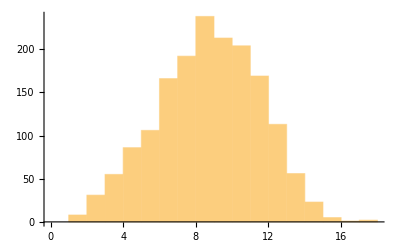

```mathematica
Histogram[lengthofTweet]
```

Let’s perform clustering with all the tweets using cosineDist.  You will notice that we get 4 clusters.

```mathematica
c = FindClusters[clean2Data,DistanceFunction->cosineDist]
```

```mathematica
Length[c[[1]]]
```

985

```mathematica
Length[c[[2]]]
```

276

```mathematica
Length[c[[3]]]
```

407

We save our clusters as a mathematica variable but also in text documents

```mathematica
Save["BrexitClusters",c]
```

```mathematica
Export["brexitClustersC1.txt",c[[1]]]
```

brexitClustersC1.txt

```mathematica
Export["brexitClustersC2.txt",c[[2]]]
Export["brexitClustersC3.txt",c[[3]]]
```

```mathematica
CosineDistance
```

```mathematica
<< BrexitClusters
```

Sample of what cluster 2 contains

```mathematica
c[[2]][[1;;50]]
```

{{rich,come,remain,nh,school,etc,nt,affect,afford,privat,leav},{leav,retweet,go,tomorrow,takecontrol,projecthop},{agre,tomorrow,chanc,leav},{leav,starter,pack},{eu,confirm,referendumorm,leav,control},{leav,remain},{go,wors,leav},{leav,said,pai,tomorrow,chanc,takebackcontrol},{leav,win,vote,rememb,acknowledg,god,merci,nation,guid,leader,choic},{wow,final,vote,freedom,democraci,independ,leav,uk},{juncker,uk,voter,know,kind,renegoti,fight,leav},{eu,referendumorm,uk,leav,unreferendumorm,lexit,snpout},{leav,pathet,think,go,rig,vote,clearli,confid,remain},{hope,leav,carri,like,eu,unmitig,disast},{want,leav,eu,sun,newspap,support,need,valid,reason,remain,just},{good,hear,bnp,mention,bbcdebat,issu,remain,tri,us,smear,leav},{plane,leav,banner,fli,directli,jo,cox,memori,trafalgar,sq,actual,troll,funer},{promot,remain,time,tl,todai,leav,dodgi},{feel,incred,proud,leav,campaign,led,team,haringei,tomorrow},{leav,insist,eu,nation,uk,abl,stai,immigr,lawyer,sai,simpl},{care,nh,pleas,end,unfair,eu,chanc,leav,thank},{like,muslim,leav},{c4debat,labour,voter,shock,secur,worker,right,eu,takebackcontrol,leav},{half,brain,vote,remain,leader,know,mind,offer,empti,promis,leav},{joepattinson,eu,loserdom,leav},{bold,brave,believ,leav,goodnight,,pleas,globe},{leav,break,eu,open,new,membership,talk,turkei,june,30th},{follow,leav,remain,campaign,chose,month,research,want,uk,great},{shall,independencedai,leav},{islington,elitist,take,moment,speak,littl,peopl,provinc,leav,takebackcontrol},{sum,debat,perfectli,imo,vote,leav,remain},{yeah,understand,set,leav,due,fact,dad,incom,affect,eu,regul,fish},{watch,cast,vote,god,sake,throw,awai,countri,leav},{sad,legitim,reason,peopl,vote,leav},{uk,voter,pleas,vote,leav,tomorrow,million,fought,di,democraci,throw,awai},{uk,stai,leav},{proeu,labour,campaign,sai,go,wooooh,attract,prospect,peopl,leav},{sjpowel,sky,new,just,poll,expert,sai,weight,leav},{leav,light,end,tunnel,tomorrow,brighter,futur,c4debat},{bruh,acc,scare,leav,win,pleas,uk,public,remain},{leav,implement,australian,style,pointsbas,immigr,system,takecontrol},{eu,leav},{undecid,vote,leav,wai,ticket,remain,room,decid,futur},{leav,takebackcontrol},{vote,leav,todai,remain,lock,car,driven,uncertain,direct},{road,diverg,wood,took,travel,differ,leav},{leav,read,german,industri,call,free,trade,deal,tomorrow},{choos,hope,fear,democraci,bureaucraci,opportun,obfusc,leav},{read,peopl,referendumerendum,britexit,leav,ukindepend},{futur,gener,elect,meaningless,unless,takebackcontrol,leav,law}}

```mathematica
<< cleanDataBrexit
```

```mathematica
<< FinalCleanBrexit
```

What if we allow only tweets with at least 4 words? We get only 2 clusters, but cluster 2 has only one tweet.

```mathematica
onlyTweet4orMore = Select[clean2Data, Length[#] ≥ 4 &]
```

{{brexit,episod,delai,thur,share,like,hell},{rich,come,remain,nh,school,etc,nt,affect,afford,privat,leav},1570,{million,tweet,leav,trend},{immigg,knew,bear,referendum}}
 |  |  |  |

```mathematica
cOp = FindClusters[onlyTweet4orMore,DistanceFunction->cosineDist,Method->"Agglomerate"]
```

```mathematica
Length[cOp]
```

2

```mathematica
Length[cOp[[2]]]
```

1

```mathematica
cOp[[2]]
```

{{steve,hilton,sai,saw,foot,high,pile,paperwork,week,down,st,half,came,brussel}}

```mathematica
Length[cc4]
```

0

We also decided to use our new Jacquard distance and see how many clusters we will get.  In here, we get 2 clusters, but cluster 2 has 626 tweets.  Of course, an analysis of the tweets in same clusters should be done.  Still, it is nice to see that we didn’t get almost empty clusters

```mathematica
cJacquard= FindClusters[onlyTweet4orMore,DistanceFunction->myDistance]
```

{{{brexit,episod,delai,thur,share,like,hell},{rich,come,remain,nh,school,etc,nt,affect,afford,privat,leav},944,{half,brain,vote,remain,leader,know,mind,offer,empti},{brexit,leav,countri,need,vote,todai,make,uk,greater}},{1}}
 |  |  |  |

```mathematica
{Length[cJacquard],Length[cJacquard[[1]]],Length[cJacquard[[2]]]}
```

{2,948,626}